```mathematica
m=0.938272046;(*GeV/c^2*)
mn=1.00137842*m(*GeV/c^2*);
M=2*m+2*mn;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.100(*GeV*);
EnL=En+m;
s=m^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-m^2];
k=P*(M/Sqrt[s]);
s2=m^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(m+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(m+M)/Sqrt[s];
```

```mathematica
pp100a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100a.csv"];
pp100a=Transpose[{pp100a[[All,1]],pp100a[[All,2]]+I*pp100a[[All,3]]}];
```

```mathematica
pp100b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100b.csv"];
pp100b=Transpose[{pp100b[[All,1]],pp100b[[All,2]]+I*pp100b[[All,3]]}];
```

```mathematica
θpp100=Transpose[{pp100a[[All,1]],pp100a[[All,2]]+pp100b[[All,2]]}];
```

```mathematica
θtoq[x_]:={2 Sqrt[En^2+2*En*m] Sin[x[[1]] Pi/360],x[[2]]}
```

```mathematica
pp100=θtoq/@θpp100;
```

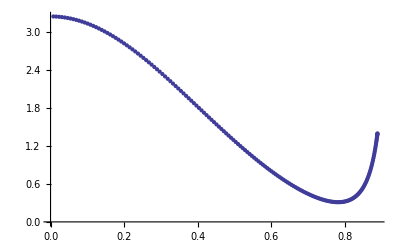

```mathematica
ListPlot[Transpose[{pp100[[All,1]],Re[pp100[[All,2]]]}]]
```

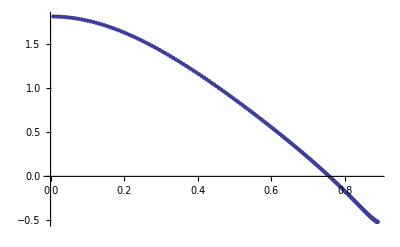

```mathematica
ListPlot[Transpose[{pp100[[All,1]],Im[pp100[[All,2]]]}]]
```

```mathematica
f=Interpolation[pp100];
```

InterpolatingFunction::dmval: Input value {0.0000181644} lies outside the range of data in the interpolating function. Extrapolation will be used.

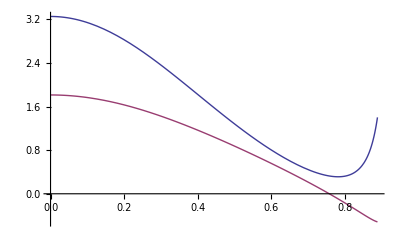

```mathematica
Plot[{Re[f[q]],Im[f[q]]},{q,0,2 P}]
```

```mathematica
Γ[b_]:=I/κ NIntegrate[BesselJ[0,b q] f[q] q,{q,0,2 P}]
Γprime[b_]:=1/(2 Pi κ) NIntegrate[q^2 Cos[ϕq] f[q],{q,0,2 P},{ϕq,0,2 Pi}]
```

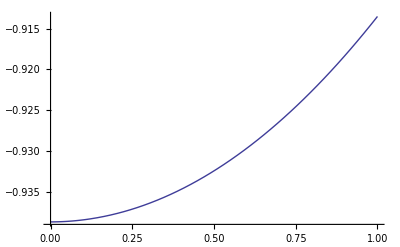

```mathematica
Plot[Re[Γ[b]],{b,0,1}]
```

```mathematica
Γ[100]
```

```mathematica
U[r_]:=I/Pi NIntegrate[(u/(1-Γ[r^2-u^2])
```

```mathematica
Integrate[Exp[-I q b Cos[ϕq]] a,{ϕq,0,2 Pi}]
```

ConditionalExpression[2 a π BesselJ[0,b q],b q∈Reals]